# Gaussian Beam Parameters

### Beam Radius w(z) vs z

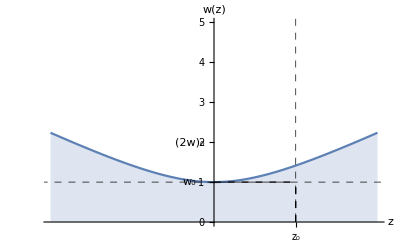

```mathematica
w[z_, w0_, zR_] := w0 Sqrt[1 + (z/zR)^2]

w0 = 1.0;    (*Initial beam waist radius*)
zR = 5.0;    (*Rayleigh range*)

Plot[w[z, w0, zR], {z, -10, 10}, PlotRange -> {{-10, 10}, {0, 5}}, 
 AxesLabel -> {"z", "w(z)"}, 
 Filling -> Axis,(*Fills area below the curve*)
 Epilog -> {Text[Subscript["w", "0"], {-1.5, w0}, {-1, 0}], 
   Text[Subscript["2w", "0"], {-1.5, 2 w0}, {-1, 0}], 
   Text["zR", {zR, -0.2}, {0, -1}], Dashed, 
   Line[{{zR, 0}, {zR, w0}}],(*Dashed line at zR*)Dashed, 
   Line[{{0, w0}, {zR, w0}}] (*Dashed line at w0*)}, 
 Ticks -> {{{zR, Subscript["z", "0"]}}, None}, 
 GridLines -> {{zR}, {w0}}, 
 GridLinesStyle -> Directive[Black, Dashed]]
```

### Radius of wavefront

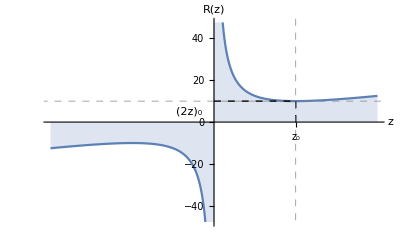

```mathematica
zR=5.0;    (*Rayleigh range*)
R[z_]:=z*(1+(zR/z)^2)

Plot[R[z],{z,-10,10},PlotRange->Automatic,AxesLabel->{"z","R(z)"},GridLinesStyle->Directive[Gray,Dashed],Filling->Axis,Epilog->{Text[Subscript["2z","0"],{-1.5,zR},{-1,0}],Dashed,Line[{{zR,0},{zR,2 zR}}],(*Dashed line at zR*)Dashed,Line[{{0,2 zR},{zR,2 zR}}] (*Dashed line at 2z0*)},Ticks->{{{zR,Subscript["z","0"]}},None},GridLines->{{zR},{2 zR}},GridLinesStyle->Directive[Black,Dashed]]
```

### Intensity of Gaussian Beam

```mathematica
(*Parameters*)I0=1.0;            (*Peak intensity*)
w0=1.0;            (*Beam waist at z=0*)
zR=Pi*w0^2/1.0; (*Rayleigh range*)


(*Beam waist as a function of z*)
w[z_]:=w0*Sqrt[1+(z/zR)^2]

(*Intensity formula*)
intensity[p_,z_]:=I0*(w0/w[z])^2*Exp[-(2 p^2)/w[z]^2]

(*Plot the intensity*)
Plot3D[intensity[p,z],{p,-5,5},{z,-10,10},PlotRange->All,AxesLabel->{"p","z","Intensity"},ColorFunction->"SunsetColors",PlotLabel->"Gaussian Beam Intensity",PlotPoints->500]
```

-Graphics3D-